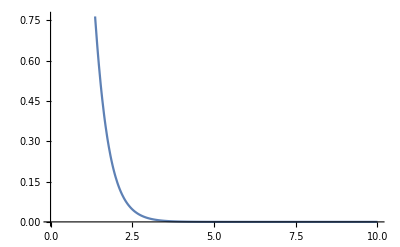

```mathematica
Clear[Θ,R,w,m,γ]
R=1;w=.4;m=1;γ=π;
Θ[r_]:=If[r==0,π,2ArcTan[Sinh[R/w]/Sinh[r/w]]];
Plot[Θ[r],{r,0,10}]
```

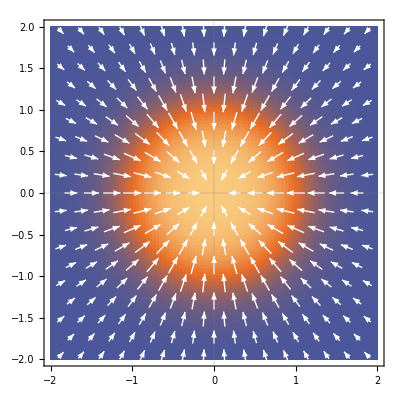

```mathematica
Clear[S,Φ,x,y]
ϕ[x_,y_]:=Arg[x+ⅈ y]
Φ[ϕ_]:=m ϕ+γ
S[r_,ϕ_]:={Sin[Θ[r]]Cos[Φ[ϕ]],Sin[Θ[r]]Sin[Φ[ϕ]],-Cos[Θ[r]]} 
Show[DensityPlot[S[√(x^2+y^2),ϕ[x,y]][[3]],{x,-2R,2R},{y,-2R,2R},MaxRecursion->2,PlotPoints->100,PlotTheme->"Scientific"],VectorPlot[S[√(x^2+y^2),ϕ[x,y]][[{1,2}]],{x,-2R,2R},{y,-2R,2R},VectorScaling->Automatic,VectorSizes->Automatic,VectorStyle->White,VectorColorFunction->None]]
```

```mathematica
data=ImportString["1,0.0,0.0,0.0,4.7383971746306486e-15,7.43572954944871e-15,0.4980530404927753
1,0.5,0.8660254037844386,0.0,-0.21208817991009032,-0.3673475032890896,0.23793206792088128
1,-0.5,0.8660254037844386,0.0,0.2120881799100971,-0.3673475032890919,0.23793206792087052
1,-1.0,0.0,0.0,0.4241763598201862,2.539323460705456e-15,0.23793206792086977
1,-0.5,-0.8660254037844386,0.0,0.21208817991009996,0.3673475032890975,0.23793206792086521
1,0.5,-0.8660254037844386,0.0,-0.2120881799100991,0.3673475032890979,0.23793206792086552
1,1.0,0.0,0.0,-0.4241763598201874,8.827682508594226e-15,0.23793206792086535
1,1.5,0.8660254037844386,0.0,-0.4209847353817898,-0.24305565029740855,0.016027813783492523
1,1.0,1.7320508075688772,0.0,-0.24210469095107362,-0.41933762547802894,-0.0634381365879438
1,0.0,1.7320508075688772,0.0,3.0589680094506022e-15,-0.4861113005948047,0.016027813783486562
1,-1.0,1.7320508075688772,0.0,0.2421046909510761,-0.4193376254780368,-0.06343813658794592
1,-1.5,0.8660254037844386,0.0,0.4209847353818004,-0.24305565029739695,0.016027813783486562
1,-2.0,0.0,0.0,0.48420938190214596,9.905338810463349e-16,-0.06343813658794624
1,-1.5,-0.8660254037844386,0.0,0.4209847353818039,0.24305565029740622,0.016027813783486666
1,-1.0,-1.7320508075688772,0.0,0.24210469095106885,0.41933762547803854,-0.0634381365879449
1,0.0,-1.7320508075688772,0.0,-6.191878607064716e-16,0.4861113005948047,0.016027813783486305
1,1.0,-1.7320508075688772,0.0,-0.24210469095107517,0.4193376254780332,-0.0634381365879482
1,1.5,-0.8660254037844386,0.0,-0.4209847353818017,0.2430556502974059,0.016027813783481316
1,2.0,0.0,0.0,-0.484209381902151,5.086371861889871e-15,-0.06343813658794048"];
latt={data[[;;,2]],data[[;;,3]],data[[;;,4]]}ᵀ;
Ss =Normalize[#]&/@({data[[;;,5]],data[[;;,6]],data[[;;,7]]}ᵀ);
```

```mathematica
data=ImportString["1,0.0,0.0,0.0,6.372506689000801e-15,-3.4949257030070235e-16,0.49805304049278604
1,0.5,0.8660254037844386,0.0,-0.212088179910085,-0.3673475032890904,0.2379320679208645
1,-0.5,0.8660254037844386,0.0,0.21208817991009676,-0.3673475032890743,0.23793206792085667
1,-1.0,0.0,0.0,0.4241763598201812,-4.1819033045481513e-16,0.23793206792085209
1,-0.5,-0.8660254037844386,0.0,0.21208817991009257,0.3673475032890841,0.23793206792085556
1,0.5,-0.8660254037844386,0.0,-0.21208817991008788,0.3673475032890725,0.2379320679208631
1,1.0,0.0,0.0,-0.4241763598201702,1.2284010614260765e-16,0.23793206792086202
1,1.5,0.8660254037844386,0.0,-0.4209847353817925,-0.24305565029739323,0.016027813783487353
1,1.0,1.7320508075688772,0.0,-0.2421046909510631,-0.4193376254780036,-0.06343813658794292
1,0.0,1.7320508075688772,0.0,2.471330431963459e-15,-0.48611130059479835,0.01602781378348675
1,-1.0,1.7320508075688772,0.0,0.24210469095106812,-0.41933762547801723,-0.06343813658794499
1,-1.5,0.8660254037844386,0.0,0.42098473538179504,-0.2430556502973975,0.016027813783485455
1,-2.0,0.0,0.0,0.48420938190212925,-2.1120427726607077e-16,-0.06343813658794589
1,-1.5,-0.8660254037844386,0.0,0.42098473538179737,0.24305565029739354,0.016027813783485674
1,-1.0,-1.7320508075688772,0.0,0.24210469095105983,0.41933762547799946,-0.06343813658794527
1,0.0,-1.7320508075688772,0.0,2.1754516590921646e-15,0.4861113005947818,0.01602781378348679
1,1.0,-1.7320508075688772,0.0,-0.24210469095106255,0.4193376254780081,-0.06343813658794317
1,1.5,-0.8660254037844386,0.0,-0.4209847353817844,0.2430556502974044,0.01602781378348673
1,2.0,0.0,0.0,-0.4842093819021197,2.3787395664331967e-16,-0.06343813658795733
1,-3.5,2.598076211353316,0.0,0.0,0.0,-1.0
1,-3.0,3.4641016151377544,0.0,0.0,0.0,-1.0
1,-4.0,3.4641016151377544,0.0,0.0,0.0,-1.0
1,-4.5,2.598076211353316,0.0,0.0,0.0,-1.0
1,-4.0,1.7320508075688774,0.0,0.0,0.0,-1.0
1,-3.0,1.7320508075688774,0.0,0.0,0.0,-1.0
1,-2.5,2.598076211353316,0.0,0.0,0.0,-1.0
1,-2.0,3.4641016151377544,0.0,0.0,0.0,-1.0
1,-2.5,4.330127018922193,0.0,0.0,0.0,-1.0
1,-3.5,4.330127018922193,0.0,0.0,0.0,-1.0
1,-4.5,4.330127018922193,0.0,0.0,0.0,-1.0
1,-5.0,3.4641016151377544,0.0,0.0,0.0,-1.0
1,-5.5,2.598076211353316,0.0,0.0,0.0,-1.0
1,-5.0,1.7320508075688774,0.0,0.0,0.0,-1.0
1,-4.5,0.8660254037844388,0.0,0.0,0.0,-1.0
1,-3.5,0.8660254037844388,0.0,0.0,0.0,-1.0
1,-2.5,0.8660254037844388,0.0,0.0,0.0,-1.0
1,-2.0,1.7320508075688774,0.0,0.0,0.0,-1.0
1,-1.5,2.598076211353316,0.0,0.0,0.0,-1.0
1,-4.0,-1.7320508075688772,0.0,0.0,0.0,-1.0
1,-3.5,-0.8660254037844386,0.0,0.0,0.0,-1.0
1,-4.5,-0.8660254037844386,0.0,0.0,0.0,-1.0
1,-5.0,-1.7320508075688772,0.0,0.0,0.0,-1.0
1,-4.5,-2.598076211353316,0.0,0.0,0.0,-1.0
1,-3.5,-2.598076211353316,0.0,0.0,0.0,-1.0
1,-3.0,-1.7320508075688772,0.0,0.0,0.0,-1.0
1,-2.5,-0.8660254037844386,0.0,0.0,0.0,-1.0
1,-3.0,0.0,0.0,0.0,0.0,-1.0
1,-4.0,0.0,0.0,0.0,0.0,-1.0
1,-5.0,0.0,0.0,0.0,0.0,-1.0
1,-5.5,-0.8660254037844386,0.0,0.0,0.0,-1.0
1,-6.0,-1.7320508075688772,0.0,0.0,0.0,-1.0
1,-5.5,-2.598076211353316,0.0,0.0,0.0,-1.0
1,-5.0,-3.4641016151377544,0.0,0.0,0.0,-1.0
1,-4.0,-3.4641016151377544,0.0,0.0,0.0,-1.0
1,-3.0,-3.4641016151377544,0.0,0.0,0.0,-1.0
1,-2.5,-2.598076211353316,0.0,0.0,0.0,-1.0
1,-2.0,-1.7320508075688772,0.0,0.0,0.0,-1.0
1,-0.5,-4.330127018922193,0.0,0.0,0.0,-1.0
1,0.0,-3.4641016151377544,0.0,0.0,0.0,-1.0
1,-1.0,-3.4641016151377544,0.0,0.0,0.0,-1.0
1,-1.5,-4.330127018922193,0.0,0.0,0.0,-1.0
1,-1.0,-5.196152422706631,0.0,0.0,0.0,-1.0
1,0.0,-5.196152422706631,0.0,0.0,0.0,-1.0
1,0.5,-4.330127018922193,0.0,0.0,0.0,-1.0
1,1.0,-3.4641016151377544,0.0,0.0,0.0,-1.0
1,0.5,-2.5980762113533156,0.0,0.0,0.0,-1.0
1,-0.5,-2.5980762113533156,0.0,0.0,0.0,-1.0
1,-1.5,-2.5980762113533156,0.0,0.0,0.0,-1.0
1,-2.0,-3.4641016151377544,0.0,0.0,0.0,-1.0
1,-2.5,-4.330127018922193,0.0,0.0,0.0,-1.0
1,-2.0,-5.196152422706631,0.0,0.0,0.0,-1.0
1,-1.5,-6.0621778264910695,0.0,0.0,0.0,-1.0
1,-0.5,-6.0621778264910695,0.0,0.0,0.0,-1.0
1,0.5,-6.0621778264910695,0.0,0.0,0.0,-1.0
1,1.0,-5.196152422706631,0.0,0.0,0.0,-1.0
1,1.5,-4.330127018922193,0.0,0.0,0.0,-1.0
1,3.5,-2.598076211353316,0.0,0.0,0.0,-1.0
1,4.0,-1.7320508075688774,0.0,0.0,0.0,-1.0
1,3.0,-1.7320508075688774,0.0,0.0,0.0,-1.0
1,2.5,-2.598076211353316,0.0,0.0,0.0,-1.0
1,3.0,-3.4641016151377544,0.0,0.0,0.0,-1.0
1,4.0,-3.4641016151377544,0.0,0.0,0.0,-1.0
1,4.5,-2.598076211353316,0.0,0.0,0.0,-1.0
1,5.0,-1.7320508075688774,0.0,0.0,0.0,-1.0
1,4.5,-0.8660254037844388,0.0,0.0,0.0,-1.0
1,3.5,-0.8660254037844388,0.0,0.0,0.0,-1.0
1,2.5,-0.8660254037844388,0.0,0.0,0.0,-1.0
1,2.0,-1.7320508075688774,0.0,0.0,0.0,-1.0
1,1.5,-2.598076211353316,0.0,0.0,0.0,-1.0
1,2.0,-3.4641016151377544,0.0,0.0,0.0,-1.0
1,2.5,-4.330127018922193,0.0,0.0,0.0,-1.0
1,3.5,-4.330127018922193,0.0,0.0,0.0,-1.0
1,4.5,-4.330127018922193,0.0,0.0,0.0,-1.0
1,5.0,-3.4641016151377544,0.0,0.0,0.0,-1.0
1,5.5,-2.598076211353316,0.0,0.0,0.0,-1.0
1,4.0,1.7320508075688772,0.0,0.0,0.0,-1.0
1,4.5,2.598076211353316,0.0,0.0,0.0,-1.0
1,3.5,2.598076211353316,0.0,0.0,0.0,-1.0
1,3.0,1.7320508075688772,0.0,0.0,0.0,-1.0
1,3.5,0.8660254037844386,0.0,0.0,0.0,-1.0
1,4.5,0.8660254037844386,0.0,0.0,0.0,-1.0
1,5.0,1.7320508075688772,0.0,0.0,0.0,-1.0
1,5.5,2.598076211353316,0.0,0.0,0.0,-1.0
1,5.0,3.4641016151377544,0.0,0.0,0.0,-1.0
1,4.0,3.4641016151377544,0.0,0.0,0.0,-1.0
1,3.0,3.4641016151377544,0.0,0.0,0.0,-1.0
1,2.5,2.598076211353316,0.0,0.0,0.0,-1.0
1,2.0,1.7320508075688772,0.0,0.0,0.0,-1.0
1,2.5,0.8660254037844386,0.0,0.0,0.0,-1.0
1,3.0,0.0,0.0,0.0,0.0,-1.0
1,4.0,0.0,0.0,0.0,0.0,-1.0
1,5.0,0.0,0.0,0.0,0.0,-1.0
1,5.5,0.8660254037844386,0.0,0.0,0.0,-1.0
1,6.0,1.7320508075688772,0.0,0.0,0.0,-1.0
1,0.5,4.330127018922193,0.0,0.0,0.0,-1.0
1,1.0,5.196152422706631,0.0,0.0,0.0,-1.0
1,0.0,5.196152422706631,0.0,0.0,0.0,-1.0
1,-0.5,4.330127018922193,0.0,0.0,0.0,-1.0
1,0.0,3.4641016151377544,0.0,0.0,0.0,-1.0
1,1.0,3.4641016151377544,0.0,0.0,0.0,-1.0
1,1.5,4.330127018922193,0.0,0.0,0.0,-1.0
1,2.0,5.196152422706631,0.0,0.0,0.0,-1.0
1,1.5,6.0621778264910695,0.0,0.0,0.0,-1.0
1,0.5,6.0621778264910695,0.0,0.0,0.0,-1.0
1,-0.5,6.0621778264910695,0.0,0.0,0.0,-1.0
1,-1.0,5.196152422706631,0.0,0.0,0.0,-1.0
1,-1.5,4.330127018922193,0.0,0.0,0.0,-1.0
1,-1.0,3.4641016151377544,0.0,0.0,0.0,-1.0
1,-0.5,2.5980762113533156,0.0,0.0,0.0,-1.0
1,0.5,2.5980762113533156,0.0,0.0,0.0,-1.0
1,1.5,2.5980762113533156,0.0,0.0,0.0,-1.0
1,2.0,3.4641016151377544,0.0,0.0,0.0,-1.0
1,2.5,4.330127018922193,0.0,0.0,0.0,-1.0"];
latt={data[[;;,2]],data[[;;,3]],data[[;;,4]]}ᵀ;
Ss =Normalize[#]&/@({data[[;;,5]],data[[;;,6]],data[[;;,7]]}ᵀ);
Ss =#&/@({data[[;;,5]],data[[;;,6]],data[[;;,7]]}ᵀ);
```

```mathematica
data=ImportString["50,0.0,0.0,0.0,1.0184595101620259e-14,1.493666992988694e-17,-0.1301222000470975
50,0.5,0.8660254037844386,0.0,1.6171337214123454e-14,2.1114342453712752e-14,-0.009036748132567253
50,-0.5,0.8660254037844386,0.0,3.614774786663829e-14,-7.214424048955989e-15,-0.00903674813256726
50,-1.0,0.0,0.0,2.946547541891432e-14,-2.8307755842270614e-14,-0.009036748132567211
50,-0.5,-0.8660254037844386,0.0,2.78217092337662e-15,-2.1094092069129367e-14,-0.009036748132567291
50,0.5,-0.8660254037844386,0.0,-1.7220827366238076e-14,7.240705234966725e-15,-0.009036748132567234
50,1.0,0.0,0.0,-1.0513227652811491e-14,2.8356918739334168e-14,-0.009036748132567255
50,1.5,0.8660254037844386,0.0,2.6143609778768546e-15,1.72067432633322e-14,0.2589435394839724
50,1.0,1.7320508075688772,0.0,8.371452063109447e-15,7.814198001819715e-15,0.355113575323106
50,0.0,1.7320508075688772,0.0,1.8868500470348487e-14,4.8498111545933576e-15,0.25894353948397236
50,-1.0,1.7320508075688772,0.0,1.5762491273141318e-14,-2.652733170428493e-15,0.35511357532310595
50,-1.5,0.8660254037844386,0.0,2.3480649882929528e-14,-1.2363592411314951e-14,0.2589435394839724
50,-2.0,0.0,0.0,1.3286905662714587e-14,-1.0475273587176232e-14,0.355113575323106
50,-1.5,-0.8660254037844386,0.0,1.1877738516797079e-14,-1.7203109170279038e-14,0.2589435394839724
50,-1.0,-1.7320508075688772,0.0,3.3952452800688444e-15,-7.800897511566834e-15,0.35511357532310595
50,0.0,-1.7320508075688772,0.0,-4.396945330088802e-15,-4.824654004569673e-15,0.2589435394839723
50,1.0,-1.7320508075688772,0.0,-3.997947795112802e-15,2.6867593306668616e-15,0.355113575323106
50,1.5,-0.8660254037844386,0.0,-9.00670259684577e-15,1.2392963016175278e-14,0.2589435394839725
50,2.0,0.0,0.0,-1.5028346457013042e-15,1.0483045311379636e-14,0.35511357532310606
50,-2.5,0.8660254037844388,0.0,0.0,0.0,1.0
50,-2.0,1.7320508075688774,0.0,0.0,0.0,1.0
50,-1.5,2.598076211353316,0.0,0.0,0.0,1.0
50,-2.5,-0.8660254037844386,0.0,0.0,0.0,1.0
50,-3.0,0.0,0.0,0.0,0.0,1.0
50,-2.0,-1.7320508075688772,0.0,0.0,0.0,1.0
50,0.5,-2.5980762113533156,0.0,0.0,0.0,1.0
50,-0.5,-2.5980762113533156,0.0,0.0,0.0,1.0
50,-1.5,-2.5980762113533156,0.0,0.0,0.0,1.0
50,2.5,-0.8660254037844388,0.0,0.0,0.0,1.0
50,2.0,-1.7320508075688774,0.0,0.0,0.0,1.0
50,1.5,-2.598076211353316,0.0,0.0,0.0,1.0
50,2.0,1.7320508075688772,0.0,0.0,0.0,1.0
50,2.5,0.8660254037844386,0.0,0.0,0.0,1.0
50,3.0,0.0,0.0,0.0,0.0,1.0
50,-0.5,2.5980762113533156,0.0,0.0,0.0,1.0
50,0.5,2.5980762113533156,0.0,0.0,0.0,1.0
50,1.5,2.5980762113533156,0.0,0.0,0.0,1.0"];
latt={data[[;;,2]],data[[;;,3]],data[[;;,4]]}ᵀ;
Ss =Normalize[#]&/@({data[[;;,5]],data[[;;,6]],data[[;;,7]]}ᵀ);
```

```mathematica
(* Discretize the field *)
L1=8;
L2=8;
a1={1.,0,0};
a2=1/2{1,√3,0}//N;
latt =Flatten[Table[a1*l1+a2*l2,{l1,-L1,L1},{l2,-L2,L2}],1];
Ss = Table[S[√(v[[1]]^2+v[[2]]^2),ϕ[v[[1]],v[[2]]]],{v,latt}];
(*Ss = Table[{0,0,1},{v,latt}];*)
```

```mathematica
data=ImportString["86,0.0,0.0,0.0,-2.1533663576618813e-16,9.495308728954723e-16,-0.0027233226300895997
86,0.5,0.8660254037844386,0.0,-4.192738883184789e-13,-1.9995900496756107e-15,0.11744152705890756
86,-0.5,0.8660254037844386,0.0,-1.937905401336092e-13,-7.840921799137839e-14,0.11702681877850624
86,-1.0,0.0,0.0,2.241368464117124e-13,-7.529395856980585e-14,0.1170631752462335
86,-0.5,-0.8660254037844386,0.0,4.189860445376899e-13,3.66494533545662e-15,0.11744152705890834
86,0.5,-0.8660254037844386,0.0,1.9442170037696095e-13,7.942827711795483e-14,0.11702681877850826
86,1.0,0.0,0.0,-2.2549680399257637e-13,7.698029997896533e-14,0.11706317524623484
86,1.5,0.8660254037844386,0.0,-1.5322843654986907e-13,1.4826166825622922e-14,0.2849299320434473
86,1.0,1.7320508075688772,0.0,-1.3907589528697214e-13,-1.4802528119411635e-15,0.3716665905277194
86,0.0,1.7320508075688772,0.0,-1.4495989886472375e-13,-2.1472241927378165e-14,0.28470612822810143
86,-1.0,1.7320508075688772,0.0,-6.281651559269454e-14,-2.5293419720771694e-14,0.3365352745657922
86,-1.5,0.8660254037844386,0.0,8.418693274874492e-15,-3.5742332692390945e-14,0.2823770631538937
86,-2.0,0.0,0.0,7.605966006756725e-14,-2.3260130149963284e-14,0.33961515171247025
86,-1.5,-0.8660254037844386,0.0,1.5322425967376827e-13,-1.4199533065551401e-14,0.28492993204344674
86,-1.0,-1.7320508075688772,0.0,1.3883015444515642e-13,2.1971046616734624e-15,0.3716665905277198
86,0.0,-1.7320508075688772,0.0,1.4458021988813648e-13,2.2531723420237663e-14,0.28470612822810315
86,1.0,-1.7320508075688772,0.0,6.219336303607995e-14,2.6220314346035604e-14,0.33653527456579374
86,1.5,-0.8660254037844386,0.0,-8.715179003270707e-15,3.690948682465947e-14,0.28237706315389527
86,2.0,0.0,0.0,-7.57630878849452e-14,2.39232510857568e-14,0.33961515171247086
86,-2.5,0.8660254037844388,0.0,0.0,0.0,1.0
86,-2.0,1.7320508075688774,0.0,0.0,0.0,1.0
86,-1.5,2.598076211353316,0.0,0.0,0.0,1.0
86,-2.5,-0.8660254037844386,0.0,0.0,0.0,1.0
86,-3.0,0.0,0.0,0.0,0.0,1.0
86,-2.0,-1.7320508075688772,0.0,0.0,0.0,1.0
86,0.5,-2.5980762113533156,0.0,0.0,0.0,1.0
86,-0.5,-2.5980762113533156,0.0,0.0,0.0,1.0
86,-1.5,-2.5980762113533156,0.0,0.0,0.0,1.0
86,2.5,-0.8660254037844388,0.0,0.0,0.0,1.0
86,2.0,-1.7320508075688774,0.0,0.0,0.0,1.0
86,1.5,-2.598076211353316,0.0,0.0,0.0,1.0
86,2.0,1.7320508075688772,0.0,0.0,0.0,1.0
86,2.5,0.8660254037844386,0.0,0.0,0.0,1.0
86,3.0,0.0,0.0,0.0,0.0,1.0
86,-0.5,2.5980762113533156,0.0,0.0,0.0,1.0
86,0.5,2.5980762113533156,0.0,0.0,0.0,1.0
86,1.5,2.5980762113533156,0.0,0.0,0.0,1.0"];
latt={data[[;;,2]],data[[;;,3]],data[[;;,4]]}ᵀ;
Ss =Normalize[#]&/@({data[[;;,5]],data[[;;,6]],data[[;;,7]]}ᵀ);
```

```mathematica
data=ImportString["89,0.0,0.0,0.0,-5.269113880515963e-15,1.233260826764107e-15,-0.023439716840730918
89,0.5,0.8660254037844386,0.0,8.70557828687284e-14,1.3856244019189692e-13,0.08873660678091322
89,-0.5,0.8660254037844386,0.0,5.6645000297032606e-14,1.4063001598999577e-14,0.08873660678092099
89,-1.0,0.0,0.0,-1.2199013140035034e-14,-1.1910532033685627e-13,0.08873660678093784
89,-0.5,-0.8660254037844386,0.0,-6.775426202202678e-14,-1.416695075195564e-13,0.088736606780913
89,0.5,-0.8660254037844386,0.0,-3.7215807848750905e-14,-1.1069634583639637e-14,0.08873660678092005
89,1.0,0.0,0.0,3.307593155795544e-14,1.1877468821154248e-13,0.0887366067809367
89,1.5,0.8660254037844386,0.0,5.2955777944195126e-14,1.3544694357337359e-13,0.3055611652198667
89,1.0,1.7320508075688772,0.0,4.7877828268458946e-14,8.912390062869774e-14,0.3596088474726419
89,0.0,1.7320508075688772,0.0,4.2896295857520194e-14,3.5838429402321214e-14,0.3055611652198218
89,-1.0,1.7320508075688772,0.0,2.7445715759959832e-14,7.38755678403796e-15,0.3596088474726684
89,-1.5,0.8660254037844386,0.0,2.169492826317862e-14,-1.0641841418628863e-14,0.305561165219888
89,-2.0,0.0,0.0,-1.6006089418990788e-14,-7.457253955538893e-14,0.35960884747271377
89,-1.5,-0.8660254037844386,0.0,-4.877302144853322e-14,-1.353463398553235e-13,0.3055611652198671
89,-1.0,-1.7320508075688772,0.0,-5.100069607749067e-14,-8.960085726807653e-14,0.3596088474726418
89,0.0,-1.7320508075688772,0.0,-3.6963227173152716e-14,-3.417530965203847e-14,0.3055611652198214
89,1.0,-1.7320508075688772,0.0,-2.9504426221066296e-14,-7.312013875249754e-15,0.35960884747266786
89,1.5,-0.8660254037844386,0.0,-1.681155646638731e-14,9.645256239801874e-15,0.30556116521988735
89,2.0,0.0,0.0,1.3305253226941365e-14,7.321088743505185e-14,0.35960884747271316
89,-2.5,0.8660254037844388,0.0,0.0,0.0,1.0
89,-2.0,1.7320508075688774,0.0,0.0,0.0,1.0
89,-1.5,2.598076211353316,0.0,0.0,0.0,1.0
89,-2.5,-0.8660254037844386,0.0,0.0,0.0,1.0
89,-3.0,0.0,0.0,0.0,0.0,1.0
89,-2.0,-1.7320508075688772,0.0,0.0,0.0,1.0
89,0.5,-2.5980762113533156,0.0,0.0,0.0,1.0
89,-0.5,-2.5980762113533156,0.0,0.0,0.0,1.0
89,-1.5,-2.5980762113533156,0.0,0.0,0.0,1.0
89,2.5,-0.8660254037844388,0.0,0.0,0.0,1.0
89,2.0,-1.7320508075688774,0.0,0.0,0.0,1.0
89,1.5,-2.598076211353316,0.0,0.0,0.0,1.0
89,2.0,1.7320508075688772,0.0,0.0,0.0,1.0
89,2.5,0.8660254037844386,0.0,0.0,0.0,1.0
89,3.0,0.0,0.0,0.0,0.0,1.0
89,-0.5,2.5980762113533156,0.0,0.0,0.0,1.0
89,0.5,2.5980762113533156,0.0,0.0,0.0,1.0
89,1.5,2.5980762113533156,0.0,0.0,0.0,1.0"];
latt={data[[;;,2]],data[[;;,3]],data[[;;,4]]}ᵀ;
Ss =Normalize[#]&/@({data[[;;,5]],data[[;;,6]],data[[;;,7]]}ᵀ);
```

```mathematica
Graphics3D[{Point[{#[[1,1]],#[[1,2]],0}],Cone[{{#[[1,1]],#[[1,2]],0}-0.25#[[2]],{#[[1,1]],#[[1,2]],0}+0.25#[[2]]},0.4]}&/@({latt,Ss}ᵀ),ImageSize->800,ViewPoint->Top]
Show[%,Graphics3D[Text[#,latt[[#]]]&/@Range[Length[latt]]]];
dist[n1_,n2_]:=Norm[n2-n1];
dists=Outer[dist,latt,latt,1];
ddists=DeleteDuplicates[Chop[dists//Flatten]]//Sort;
(*neighbors={#,#}&/@latt[[All,1]];*)
neighbors=First[Position[dists,x_/;Abs[x-#]<1*^-8,3]&/@ddists[[{2,1}]]];//AbsoluteTiming;
nnPlot=Graphics3D[{{Black,CapForm["Butt"],Tube[{latt[[#[[1]]]],latt[[#[[2]]]]},0.1]}&/@neighbors},ViewPoint->Top];

triangle[s1_,s2_]:=If[Length[cs=Intersection[s1,s2]]==1&&dist[latt[[s1[[1]]]],latt[[s2[[1]]]]]<=1.&&dist[latt[[s1[[2]]]],latt[[s2[[1]]]]]<=1.&&dist[latt[[s1[[2]]]],latt[[s2[[2]]]]]<=1.&&dist[latt[[s1[[1]]]],latt[[s2[[2]]]]]<=1.,{First[cs],First[Complement[s1,s2]],First[Complement[s2,s1]]},Nothing]

triangles=DeleteDuplicates[Flatten[Outer[triangle,neighbors,neighbors,1],1]];
(triangles//Length)
%/6
Clear[X,i1,i2,i3]
X[i1_,i2_,i3_]:=1+Ss[[i1]].Ss[[i2]]+Ss[[i2]].Ss[[i3]] + Ss[[i3]].Ss[[i1]]
Y[i1_,i2_,i3_]:=Ss[[i1]].(Ss[[i2]]×Ss[[i3]])
signY[i1_,i2_,i3_]:=Ss[[i1]].(Ss[[i2]]×Ss[[i3]])*Sign[((latt[[i2]]-latt[[i1]])×(latt[[i3]]-latt[[i2]]))[[3]]]
A[i1_,i2_,i3_]:=2Arg[X[i1,i2,i3]+ⅈ Y[i1,i2,i3]]*Sign[((latt[[i2]]-latt[[i1]])×(latt[[i3]]-latt[[i2]]))[[3]]]
(* topological charge for the spin profile *)
topoDensity=Total[signY[Sequence@@#]&/@triangles]/6/4/π
topoCharge=Total[A[Sequence@@#]&/@triangles]/6/4/π
```

-Graphics3D-

324

54

6.84687×10^-25

1.5

```mathematica
Chop[A[Sequence@@#]&/@triangles]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3.14159,3.14159,0,0,3.14159,3.14159,3.14159,3.14159,3.14159,3.14159,3.14159,3.14159,3.14159,3.14159,3.14159,3.14159,3.14159,3.14159,0,0,-3.14159,-3.14159,3.14159,3.14159,-3.14159,-3.14159,-3.14159,-3.14159,-3.14159,-3.14159,-3.14159,-3.14159,-3.14159,-3.14159,0,0,0,0,-3.14159,-3.14159,-3.14159,-3.14159,-3.14159,-3.14159,-3.14159,-3.14159,0,-3.14159,0,-3.14159,0,0,3.14159,3.14159,0,0,-3.14159,-3.14159,-3.14159,-3.14159,-3.14159,-3.14159,3.14159,-3.14159,3.14159,-3.14159,0,0,3.14159,3.14159,3.14159,3.14159,3.14159,3.14159,3.14159,3.14159,3.14159,3.14159,3.14159,3.14159,3.14159,3.14159,3.14159,3.14159,3.14159,3.14159,3.14159,3.14159,3.14159,3.14159,3.14159,3.14159,3.14159,3.14159,3.14159,3.14159,0,0,3.14159,3.14159,0,0,0,0,0,0,0,0,0,0,3.14159,3.14159,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-3.14159,-3.14159,0,0,0,0,0,0,0,0,0,0,-3.14159,-3.14159,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-3.14159,-3.14159,0,0,0,0,0,0,0,0,0,0,-3.14159,-3.14159,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-3.14159,-3.14159,0,0,0,0,0,0,0,0,0,0,-3.14159,-3.14159,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3.14159,3.14159,0,0,0,0,0,0,0,0,0,0,3.14159,3.14159,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3.14159,3.14159,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}